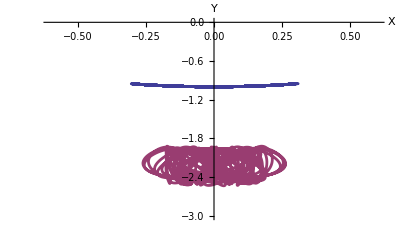

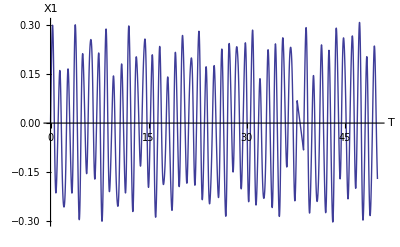

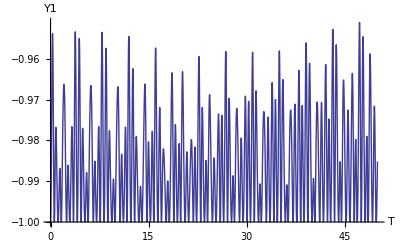

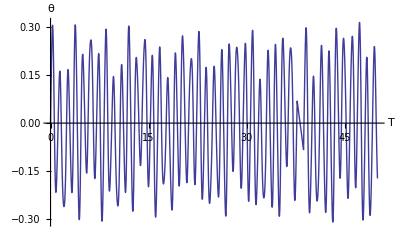

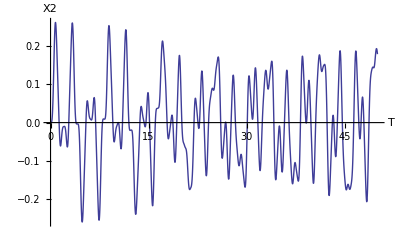

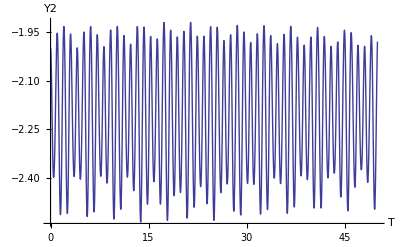

```mathematica
g=9.8;k=4;m1=0.1;m2=0.1;
L1=1;L2=1;tm=50;
initial1={0,1.4/L1};
initial3={0,0.0,-(L1+L2),0};
temp=2L1(y2[t]Cos[θ[t]]-x2[t]Sin[θ[t]]);
L=√(x2[t]^2+y2[t]^2+L1^2+temp);
equs=
{θ''[t]==
(y2[t]Sin[θ[t]]+x2[t]Cos[θ[t]])(1-L2/L)k/(m1*L1)
-g/L1 Sin[θ[t]],
x2''[t]==-(x2[t]-L1*Sin[θ[t]])(1-L2/L)k/m2,
y2''[t]==-(y2[t]+L1*Cos[θ[t]])(1-L2/L)k/m2-g,
θ[0]==initial1[[1]],θ'[0]==initial1[[2]],
x2[0]==initial3[[1]],x2'[0]==initial3[[2]],
y2[0]==initial3[[3]],y2'[0]==initial3[[4]]};
s=NDSolve[equs,{θ,x2,y2},{t,0,tm}];
{θ,x2,y2}={θ,x2,y2}/.s[[1]];
ParametricPlot[{{L1*Sin[θ[t]],-L1*Cos[θ[t]]},{x2[t],y2[t]}},{t,0,tm},
PlotRange->{{-0.6,0.6},{-3,0}},
AxesLabel->{"X","Y"},AspectRatio->0.6,
AxesStyle->Thickness[0.004],
PlotStyle->Thickness[0.005]]
Plot[L1*Sin[θ[t]],{t,0,50},AxesLabel->{"T","X1"}]
Plot[-L1*Cos[θ[t]],{t,0,50},AxesLabel->{"T","Y1"}]
Plot[θ[t],{t,0,50},AxesLabel->{"T","θ"}]
Plot[x2[t],{t,0,50},AxesLabel->{"T","X2"}]
Plot[y2[t],{t,0,50},AxesLabel->{"T","Y2"}]
Clear[g,equs,s,θ,x2,y2,initial1,initial3]
```